# Data generation

## TODO

## Exec Sequence

ClusteringValidityIndicesAntiScaleMST(def-index)_Amano-Wada.nb

/home/kamano/gitsrc/MATH_SCRIPT/SCRIPTS/Cluster+Distance_Operations.txt

ClusterValidityIndices_Base(data-generation).nb (this notebook)

ClusterValidityIndices_Base(data-clustering).nb

ClusteringValidityIndicesAntiScaleMST(create-tree)_Amano-Wada.nb

ClusteringValidityIndicesAntiScaleMST(calc-index)_Amano-Wada.nb

ClusteringValidityIndicesAntiScaleMST(sol-summary)_Amano-Wada.nb

ClusteringValidityIndicesAntiScaleMST(sol-discussion)_Amano-Wada.nb

ClusterValidityIndices_Sriparna_Exam(calc-index).nb

ClusterValidityIndices_Sriparna_Exam(summary-index).nb

## Data used for article

```mathematica
{1,2,4,5,6,7,10}
```

{1,2,4,5,6,7,10}

## Data format

### general information

Artificial data generation for clulstering varidity.

Data structire:
<Model and annotation>
;
<Dimension>[\tab]<Number of clusters>[\tab]<Number of samples>[\tab]<Number of background points>
;
<Cluster centers (model): matrix with tab delimiter>
;
<Samples: matrix with tab delimiter>
;

### answer form

< x1 >[\tab]< y2 >[\tab]...[\tab]<cl1>
< x2 >[\tab]< y2 >[\tab]...[\tab]<cl2>
...

## Preparation

```mathematica
(*dir="/Users/amanokou/gitsrc/"*)
```

```mathematica
dir="/home/kamano/gitsrc/"
```

/home/kamano/gitsrc/

```mathematica
(*dir="/Users/kouamano/gitsrc/"*)
```

```mathematica
Get[dir<>"MATH_SCRIPT/SCRIPTS/polar.txt"]
```

```mathematica
SetDirectory[dir<>"ClusteringAdequation/generative-data"]
```

/home/kamano/gitsrc/ClusteringAdequation/generative-data

## Programs

```mathematica
strDataToExportStr[n_]:=StringJoin[Riffle[{anntS[n],dimS[n],centersS[n],samplesS[n]},";\n"]]
```

```mathematica
distanceMat[mat_]:=Module[
{n},
n=Length[mat];
Table[EuclideanDistance[mat[[i]],mat[[j]]],{i,n},{j,n}]
]
```

## 2D

### data 1 (general)

```mathematica
id=1
```

1

```mathematica
anntS[id]="Model: central random, circles, one radius, triangle.\n"
```

Model: central random, circles, one radius, triangle.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
centers[id]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[id] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[id]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.73205

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/3}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

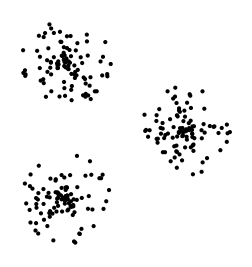

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{-0.0169398,-0.0200145}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

1.02304

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.989731,-0.00241217},{-0.496166,0.827419},{-0.544384,-0.88505}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.285134,0.292118,0.271859}

Export 4f iles:

```mathematica
Export["data1.tsv",strDataToExportStr[id],"String"]
```

data1.tsv

```mathematica
Export["data1.ans.tsv",samplesWithCl[id]]
```

data1.ans.tsv

```mathematica
Export["data1.ans.totalR",totalR[id],"Table"]
```

data1.ans.totalR

```mathematica
Export["data1.ans.clRs",clRs[id],"Table"]
```

data1.ans.clRs

### data 2 (unbalanced)

```mathematica
id=2
```

2

```mathematica
anntS[id]="Model: unbalanced central random, circles, radiuses.\n"
```

Model: unbalanced central random, circles, radiuses.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={200,100,50};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{200, 100, 50}	{0}

```mathematica
centers[id]={{0,0},{0.5,-1},{-0.5,-0.75}}
```

{{0,0},{0.5,-1},{-0.5,-0.75}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0.5	-1
-0.5	-0.75

```mathematica
distanceMat[centers[id]]
```

{{0,1.11803,0.901388},{1.11803,0.,1.03078},{0.901388,1.03078,0.}}

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]]]/(numClass[id]^2-numClass[id])
```

1.01673

```mathematica
radius[id]={distMean[id]*0.5,distMean[id]*0.35,distMean[id]*0.17}
```

{0.508366,0.355856,0.172845}

```mathematica
samples[id]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,radius[id][[n]]}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

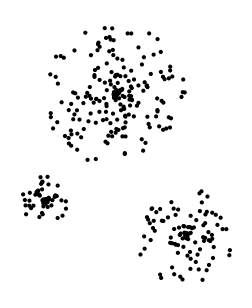

```mathematica
Graphics[Map[Point[#]&,samples[id],{2}]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id][[i]]],{i,Length[samples[id]]}],1];
```

```mathematica
totalCenter[id]=Mean[Flatten[samples[id],1]]
```

{0.0773355,-0.392963}

全サンプルの平均半径

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id],1]]]
```

0.577347

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id]]
```

{{0.00685672,-0.00270844},{0.510366,-0.999878},{-0.50681,-0.740152}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.258715,0.178183,0.0888043}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data2.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data2.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data2.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data2.ans.clRs

### data 4 (sub class)

```mathematica
id=4
```

4

```mathematica
anntS[id]="Model: central random , circles, one radius, subclusters.\n"
```

Model: central random , circles, one radius, subclusters.

```mathematica
dim[id]=2;
numClass[id]=4;
numSample[id]={100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[id]={{2,1},{2,-1},{-2,1},{-2,-1}}
```

{{2,1},{2,-1},{-2,1},{-2,-1}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

2	1
2	-1
-2	1
-2	-1

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

3.49071

```mathematica
samples[id,"class"]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/5}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{2.64758,-2.67576},{1.65689,-1.64483}}

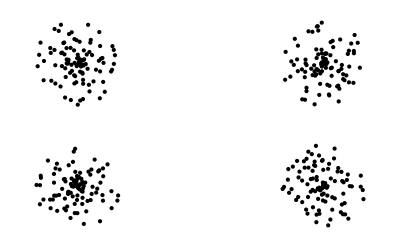

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0167978,-0.0123693}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.25351

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{2.00198,0.967732},{1.96967,-0.99472},{-2.00677,1.00302},{-2.03208,-1.02551}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.333995,0.35281,0.345239,0.320344}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data4.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data4.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data4.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data4.ans.clRs

### data 5 (ring + disc)

```mathematica
id=5
```

5

```mathematica
anntS[id]="Model: central random , disc + ring.\n"
```

Model: central random , disc + ring.

```mathematica
dim[id]=2;
numClass[id]=2;
numSample[id]={100,200};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	2	{100, 200}	{0}

```mathematica
centers[id]={{0,0},{0,0}}
```

{{0,0},{0,0}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0
0	0

```mathematica
samples[id,"disc"]=Map[polarToxy[#]&,Table[{RandomReal[{0,1}],RandomReal[{0,2 Pi}]},{numSample[id][[1]]}]];
```

```mathematica
samples[id,"ring"]=Map[polarToxy[#]&,Table[{RandomReal[{1.5,2}],RandomReal[{0,2 Pi}]},{numSample[id][[2]]}]];
```

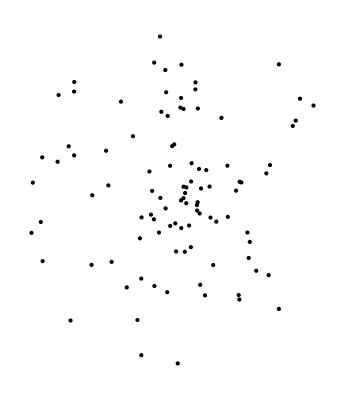

```mathematica
Graphics[Map[Point[#]&,samples[id,"disc"]]]
```

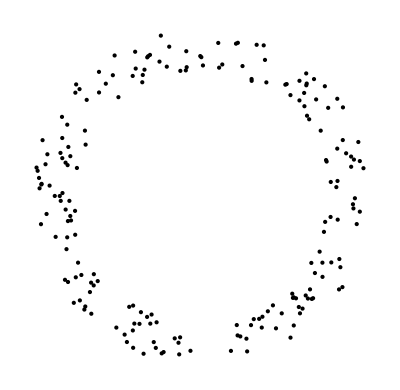

```mathematica
Graphics[Map[Point[#]&,samples[id,"ring"]]]
```

```mathematica
samples[id,"class"]=List[samples[id,"disc"],samples[id,"ring"]];
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

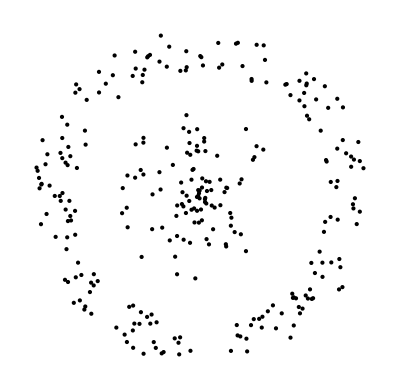

```mathematica
Map[Point[#]&,samples[id,"class"]]//Graphics
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0568171,-0.00556567}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.32132

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.081255,0.0514109},{-0.0445982,-0.034054}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.489582,1.73775}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data5.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data5.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data5.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data5.ans.clRs

### data 6 (spiral)

```mathematica
id=6
```

6

```mathematica
anntS[id]="Model: spiral x 3.\n"
```

Model: spiral x 3.

```mathematica
dim[id]=2;
numClass[id]=3;
numSample[id]={100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{0}

```mathematica
origins[id]={{0,0},{0,0},{0,0}}
```

{{0,0},{0,0},{0,0}}

```mathematica
(samples[id,0]=Map[polarToxy[#]&,Table[{r,3r},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[id,0]=Mean[samples[id,0]]
```

{0.0684864,0.339278}

```mathematica
(samples[id,1]=Map[polarToxy[#]&,Table[{r,3r+(2Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[id,1]=Mean[samples[id,1]]
```

{-0.328066,-0.110328}

```mathematica
(samples[id,2]=Map[polarToxy[#]&,Table[{r,3r+(4Pi/3)},{r,0.5,3-0.02,0.025}]])//Length
```

100

```mathematica
center[id,2]=Mean[samples[id,2]]
```

{0.25958,-0.22895}

```mathematica
centers[id]={center[id,0],center[id,1],center[id,2]}
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.06848640517315346	0.3392778825308757
-0.3280664678005077	-0.11032797457161272
0.25958006262735384	-0.22894990795926298

```mathematica
samples[id,"class"]=List[samples[id,0],samples[id,1],samples[id,2]];
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

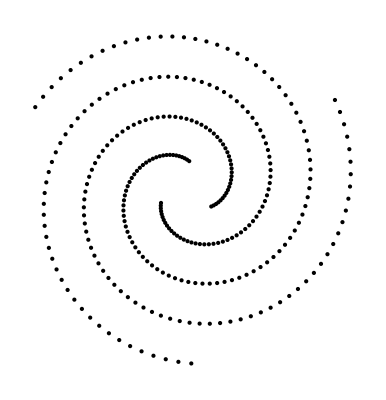

```mathematica
Map[Point[#]&,samples[id,"class"]]//Graphics
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-1.12503×10^-16,4.81097×10^-17}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.7375

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0684864,0.339278},{-0.328066,-0.110328},{0.25958,-0.22895}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.71971,1.71971,1.71971}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data6.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data6.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data6.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data6.ans.clRs

## 3D

### data 7 (chain)

```mathematica
id=7
```

7

```mathematica
anntS[id]="Model: double chain.\n"
```

Model: double chain.

```mathematica
dim[id]=3;
numClass[id]=2;
numSample[id]={150,150};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	2	{150, 150}	{0}

```mathematica
centers[id]={{0,0,0},{1,0,0}}
```

{{0,0,0},{1,0,0}}

```mathematica
(*origins[6]={{0,0},{0,0},{0,0}}*)
```

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0	0
1	0	0

```mathematica
samples[id,1]=Map[sPolarToxyz[#]&,Table[{1,Pi/2,ph},{ph,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[id,1]]//Length
```

150

```mathematica
Map[Point[#]&,samples[id,1]]//Graphics3D
```

-Graphics3D-

```mathematica
samples[id,2]=Map[sPolarToxyz[#]&,Table[{1,th,0},{th,0,2Pi-2Pi/150,2Pi/150}]];
```

```mathematica
Map[Point[#]&,samples[id,2]]//Length
```

150

```mathematica
Map[Point[#]&,samples[id,2]]//Graphics3D
```

-Graphics3D-

```mathematica
(samples[id,"class"]=List[samples[id,1],Map[#+centers[id][[2]]&,samples[id,2]]]//N)//Length
```

2

```mathematica
Map[Point[#]&,samples[id,"class"]]//Graphics3D
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.5,-2.7293×10^-18,2.96059×10^-18}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.06354

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{5.92119×10^-18,-5.4586×10^-18,0.},{1.,0.,5.92119×10^-18}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.,1.}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data7.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data7.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data7.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data7.ans.clRs

## Many classes

### data 8 (4 classes)

```mathematica
id=8
```

8

```mathematica
anntS[id]="Model: central random , circles, one radius, 2d-4class.\n"
```

Model: central random , circles, one radius, 2d-4class.

```mathematica
dim[id]=2;
numClass[id]=4;
numSample[id]={100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	4	{100, 100, 100, 100}	{0}

```mathematica
centers[id]={{2,2},{2,-2},{-2,2},{-2,-2}}
```

{{2,2},{2,-2},{-2,2},{-2,-2}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

2	2
2	-2
-2	2
-2	-2

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

4.55228

```mathematica
samples[id,"class"]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/4}],RandomReal[{0,2Pi}]}],{numSample[id][[n]]}]],{n,numClass[id]}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{3.06019,-3.07817},{3.12052,-3.07795}}

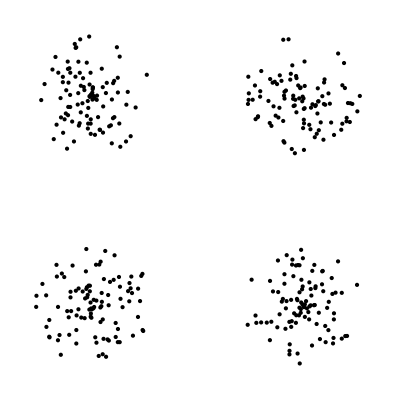

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0371424,-0.021985}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.82437

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{1.94349,1.87276},{1.98166,-1.95309},{-2.08764,1.9605},{-1.98609,-1.96812}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.608936,0.550914,0.558609,0.615257}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data8.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data8.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data8.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data8.ans.clRs

### data 9 (8 classes)

```mathematica
id=9
```

9

```mathematica
anntS[id]="Model: central random , circles, one radius, 2d-8class.\n"
```

Model: central random , circles, one radius, 2d-8class.

```mathematica
dim[id]=2;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

2	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]={{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}
```

{{7,7},{7,-7},{-7,7},{-7,-7},{0,20},{20,0},{0,-20},{-20,0}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

7	7
7	-7
-7	7
-7	-7
0	20
20	0
0	-20
-20	0

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

22.4998

```mathematica
samples[id,"class"]=Table[Map[#+centers[id][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[id]/4.2}],RandomReal[{0,2Pi}]}],{numSample[9][[n]]}]],{n,numClass[9]}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{24.1601,-25.1463},{25.078,-25.2622}}

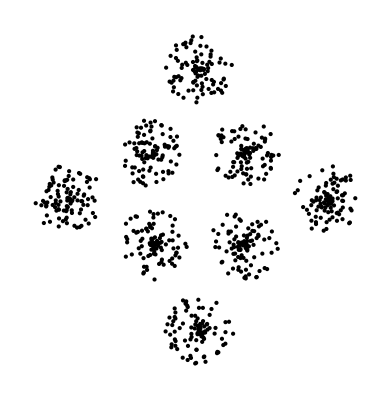

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

```mathematica
samplesS[id]=ExportString[Flatten[samples[9,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0729281,-0.0239091}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

15.2426

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{7.36682,6.9282},{6.98838,-7.19161},{-7.31663,7.25382},{-6.82729,-6.70468},{-0.188689,19.8233},{20.0447,-0.152725},{-0.387959,-20.2403},{-20.2627,0.0927074}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{2.73374,2.67365,2.75747,2.61709,2.82188,2.45491,2.86239,2.90825}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data9.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data9.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data9.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data9.ans.clRs

### data 10 (3d-8 classes) (scale: base)

```mathematica
id=10
```

10

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class (base).\n"
```

Model: central random , circles, one radius, 3d-8class (base).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]
```

{{0,0,0},{0,0,10},{0,10,0},{0,10,10},{10,0,0},{10,0,10},{10,10,0},{10,10,10}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0	0	0
0	0	10
0	10	0
0	10	10
10	0	0
10	0	10
10	10	0
10	10	10

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

12.821

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/16]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{12.0608,-1.83842},{12.7302,-2.12882},{12.5041,-2.07108}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{4.97641,5.03381,5.03971}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

8.77015

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{-0.0422536,0.0945788,0.123513},{-0.0350625,-0.0133566,9.93592},{-0.0383216,10.1056,-0.0297499},{-0.0699905,10.1214,10.046},{9.96256,-0.0855542,0.109844},{9.98334,-0.0210603,10.1276},{10.0249,10.0608,-0.027692},{10.0261,10.0081,10.0323}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{1.26715,1.26536,1.30769,1.24016,1.32604,1.32598,1.26429,1.24199}

```mathematica
Export["data"<>ToString[id]<>".tsv",strDataToExportStr[id],"String"]
```

data10.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.tsv",samplesWithCl[id]]
```

data10.ans.tsv

```mathematica
Export["data"<>ToString[id]<>".ans.totalR",totalR[id],"Table"]
```

data10.ans.totalR

```mathematica
Export["data"<>ToString[id]<>".ans.clRs",clRs[id],"Table"]
```

data10.ans.clRs

### data 10.2 (3d-8 classes) (scale: 2)

```mathematica
id=10.2
```

10.2

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled.\n"
```

Model: central random , circles, one radius, 3d-8class, scaled.

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/4//N
```

{{0.,0.,0.},{0.,0.,2.5},{0.,2.5,0.},{0.,2.5,2.5},{2.5,0.,0.},{2.5,0.,2.5},{2.5,2.5,0.},{2.5,2.5,2.5}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n";
```

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

3.20525

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/10]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{3.39644,-0.989422},{3.44774,-0.953482},{3.28624,-1.25921}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{1.24505,1.24059,1.27258}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

2.21784

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0362714,-0.0379218,-0.0315104},{-0.000954635,-0.0184705,2.53667},{-0.0137521,2.52774,0.0426337},{-0.0331122,2.48748,2.53368},{2.49872,0.0285541,0.0409621},{2.52906,-0.0277923,2.52972},{2.49837,2.50867,0.00295792},{2.4458,2.45649,2.52552}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.508798,0.460621,0.469446,0.502585,0.494691,0.514818,0.51319,0.488531}

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".tsv",strDataToExportStr[id],"String"]
```

data10-2.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.tsv",samplesWithCl[id]]
```

data10-2.ans.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.totalR",totalR[id],"Table"]
```

data10-2.ans.totalR

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.clRs",clRs[id],"Table"]
```

data10-2.ans.clRs

### data 10.3 (3d-8 classes) (scale: 3)

```mathematica
id=10.3
```

10.3

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(3).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(3).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/10]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.72728,-0.450109},{1.7627,-0.460076},{1.82365,-0.484721}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.622145,0.620535,0.631003}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.10573

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.0139431,0.0142387,-0.00464739},{-0.0316858,0.00224565,1.22593},{-0.0160377,1.25055,0.0049},{0.00615211,1.24467,1.27972},{1.23826,-0.0174238,0.0151373},{1.24875,0.000743717,1.27227},{1.26294,1.24988,0.0105855},{1.25484,1.21938,1.24413}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.241154,0.25261,0.257119,0.262453,0.246144,0.261653,0.242514,0.267577}

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".tsv",strDataToExportStr[id],"String"]
```

data10-3.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.tsv",samplesWithCl[id]]
```

data10-3.ans.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.totalR",totalR[id],"Table"]
```

data10-3.ans.totalR

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.clRs",clRs[id],"Table"]
```

data10-3.ans.clRs

### data 10.4 (3d-8 classes) (scale: 4)

```mathematica
id=10.4
```

10.4

```mathematica
anntS[id]="Model: central random , circles, one radius, 3d-8class, scaled(4).\n"
```

Model: central random , circles, one radius, 3d-8class, scaled(4).

```mathematica
dim[id]=3;
numClass[id]=8;
numSample[id]={100,100,100,100,100,100,100,100};
numBG[id]={0};
```

```mathematica
dimS[id]=StringJoin[Riffle[{ToString[dim[id]],ToString[numClass[id]],ToString[numSample[id]],ToString[numBG[id]]},"\t"],"\n"]
```

3	8	{100, 100, 100, 100, 100, 100, 100, 100}	{0}

```mathematica
centers[id]=Tuples[{0,10},3]/8//N
```

{{0.,0.,0.},{0.,0.,1.25},{0.,1.25,0.},{0.,1.25,1.25},{1.25,0.,0.},{1.25,0.,1.25},{1.25,1.25,0.},{1.25,1.25,1.25}}

```mathematica
centersS[id]=ExportString[centers[id],"TSV"]<>"\n"
```

0.	0.	0.
0.	0.	1.25
0.	1.25	0.
0.	1.25	1.25
1.25	0.	0.
1.25	0.	1.25
1.25	1.25	0.
1.25	1.25	1.25

```mathematica
distMean[id]=Tr[Flatten[distanceMat[centers[id]]//N]]/(numClass[id]^2-numClass[id])
```

1.60262

```mathematica
samples[id,"class"]=Table[centers[id][[c]]+Table[RandomVariate[NormalDistribution[0,distMean[id]/15]],{3}],{c,numClass[id]},{100}];
```

```mathematica
maxmin[id]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[id,"class"],1]]]
```

{{1.6813,-0.270737},{1.52552,-0.298271},{1.59747,-0.330163}}

```mathematica
Graphics3D[Map[Point[#]&,Flatten[samples[id,"class"],1]]]
```

-Graphics3D-

```mathematica
samplesS[id]=ExportString[Flatten[samples[id,"class"],1],"TSV"]<>"\n";
```

正解データ

```mathematica
samplesWithCl[id]=Flatten[Table[Map[Append[#,i]&,samples[id,"class"][[i]]],{i,Length[samples[id,"class"]]}],1];
```

全サンプルの平均半径

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{0.6275,0.616918,0.621226}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.09755

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.00161918,-0.0175263,-0.0076525},{-0.0175399,0.00294938,1.24067},{-0.00335542,1.25125,0.00112547},{-0.00308463,1.23802,1.24872},{1.26168,-0.0279434,-0.00526854},{1.25638,0.0148089,1.2454},{1.26008,1.24741,-0.00317538},{1.26423,1.22638,1.25}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.168443,0.162434,0.171365,0.173812,0.171367,0.17087,0.179682,0.189618}

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".tsv",strDataToExportStr[id],"String"]
```

data10-4.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.tsv",samplesWithCl[id]]
```

data10-4.ans.tsv

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.totalR",totalR[id],"Table"]
```

data10-4.ans.totalR

```mathematica
Export["data"<>StringReplace[ToString[id],"."->"-"]<>".ans.clRs",clRs[id],"Table"]
```

data10-4.ans.clRs

## Noisy

### data 3 (noisy)(old)

```mathematica
anntS[3]="Model: central random + noise, circles, one radius, triangle.\n"
```

Model: central random + noise, circles, one radius, triangle.

```mathematica
dim[3]=2;
numClass[3]=3;
numSample[3]={100,100,100};
numBG[3]={150};
```

```mathematica
dimS[3]=StringJoin[Riffle[{ToString[dim[3]],ToString[numClass[3]],ToString[numSample[3]],ToString[numBG[3]]},"\t"],"\n"]
```

2	3	{100, 100, 100}	{150}

```mathematica
centers[3]=Map[polarToxy[N[{1,#}]]&,Table[2Pi/numClass[3] n,{n,0,2}]]
```

{{1.,0.},{-0.5,0.866025},{-0.5,-0.866025}}

```mathematica
centersS[3]=ExportString[centers[3],"TSV"]<>"\n"
```

1.	0.
-0.4999999999999998	0.8660254037844387
-0.5000000000000004	-0.8660254037844384

```mathematica
distanceMat[centers[3]]
```

{{0.,1.73205,1.73205},{1.73205,0.,1.73205},{1.73205,1.73205,0.}}

```mathematica
distMean[3]=Tr[Flatten[distanceMat[centers[3]]]]/(numClass[3]^2-numClass[3])
```

1.73205

```mathematica
samples[3,"class"]=Table[Map[#+centers[3][[n]]&,Table[polarToxy[{RandomReal[{0,distMean[3]/3}],RandomReal[{0,2Pi}]}],{numSample[3][[n]]}]],{n,numClass[3]}];
```

```mathematica
maxmin[3]=Map[{Max[#],Min[#]}&,Transpose[Flatten[samples[3,"class"],1]]]
```

{{1.56435,-1.0105},{1.36032,-1.43595}}

```mathematica
samples[3,"background"]=Table[{RandomReal[maxmin[3][[1]]],RandomReal[maxmin[3][[2]]]},{numBG[3][[1]]}];
```

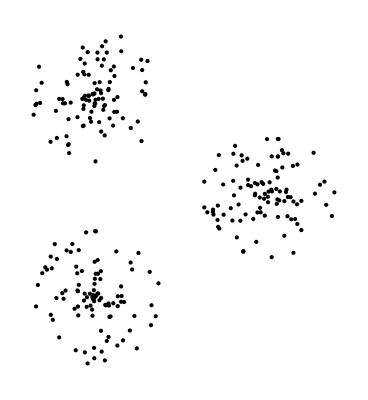

```mathematica
Graphics[Map[Point[#]&,Flatten[samples[3,"class"],1]]]
```

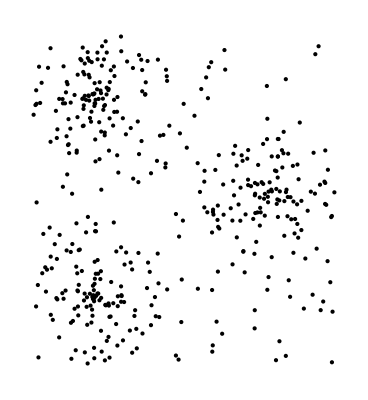

```mathematica
Graphics[Map[Point[#]&,Join[Flatten[samples[3,"class"],1],samples[3,"background"]]]]
```

```mathematica
samplesS[3]=ExportString[Join[Flatten[samples[3,"class"],1],samples[3,"background"]],"TSV"]<>"\n";
```

```mathematica
(*(samples[3,"All"]=Append[samples[3,"class"],samples[3,"background"]])//Length*)
```

全サンプルの平均半径

```mathematica
id=3
```

3

```mathematica
totalCenter[id]=Mean[Flatten[samples[id,"class"],1]]
```

{-0.0122606,0.00326999}

```mathematica
totalR[id]=Mean[Map[EuclideanDistance[totalCenter[id],#]&,Flatten[samples[id,"class"],1]]]
```

1.01003

各クラスタの平均半径

```mathematica
clCenters[id]=Map[Mean,samples[id,"class"]]
```

{{0.958673,0.0158914},{-0.500193,0.852192},{-0.495261,-0.858274}}

```mathematica
clRs[id]=Table[Map[EuclideanDistance[clCenters[id][[i]],#]&,samples[id,"class"][[i]]]//Mean,{i,Length[clCenters[id]]}]
```

{0.306362,0.275759,0.287733}

```mathematica
Export["data3.tsv",strDataToExportStr[3],"String"]
```

data3.tsv

```mathematica
Export["data3.ans.totalR",totalR[id],"Table"]
```

data3.ans.totalR

```mathematica
Export["data3.ans.clRs",clRs[id],"Table"]
```

data3.ans.clRs

## high Dimensional

## Experimental